# Code for project "Interpretation of frequency-dependent seismic responses of finely layered,partially saturated and fractured reservoirs"

#### Giorgos Papageorgiou, 10/09/2018

## 1. Multi-Fluid Auxiliary functions

```mathematica
relPermBrooksCorey[λ_,{swr_,snwr_}]:=Module[{kw, knw, seff}, 
   seff = Clip[N[(#1 - swr)/(1 - swr - snwr)],{0, 1}] & ; 
   kw = Clip[N[seff[#1]^((2 + 3*λ)/λ)],{0, 1}]&;knw = Clip[N[(1 - seff[#1])^2*(1 - seff[#1]^((2 + λ)/λ))], {0, 1}]&; {kw[#1], knw[#1]}&]; 
fluidMixModulus[K1_, K2_, s1_,q_]:=(s1 + q*(1 - s1))/(s1/K1 + q*((1 - s1)/K2))//N//Chop;
fluidMixViscosity[η1_, η2_, s1_,q_,brooksCoreyParams_:{_,{_,_}}]:=Module[{k},
k = relPermBrooksCorey@@brooksCoreyParams;(s1 + q*(1 - s1))/(k[s1][[1]]/η1 + q*(k[s1][[2]]/η2))//N//Chop
];
fluidMixRelaxation[η1_, η2_, s1_,q_,brooksCoreyParams_:{_,{_,_}}]:=fluidMixViscosity[η1, η2, s1,q,brooksCoreyParams]/η1//N//Chop;
```

### Worked Practical Examples and Code Explanation

Example 1: Brooks Corey relative permeability for various values of the pore size distribution parameter λ using function relPermBrooksCorey

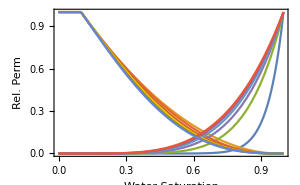

```mathematica
Plot[Evaluate@Table[relPermBrooksCorey[i,{.1,0}][s],{i,1/5,3,1/2}],{s,0,1},Frame->True, FrameLabel->{"Water Saturation","Rel. Perm"}, ImageSize->300]
```

Example 2: Mixed fluid moduli for gas-water system and different values of the capillary parameter q using fluidMixModulus

```mathematica
With[{watermod =2.4, gasmod=0.1},
Plot[Evaluate@fluidMixModulus[watermod,gasmod,s,10^Range[0,Log[10,gasmod/watermod],Log[10,gasmod/watermod]/4]],{s,0,1},PlotRange->All,Frame->True, FrameLabel->{"Water Saturation","Mixed Fluid Modulus"},PlotLabels->{"Most Uniform","q=.3","q=0.1","q=0.03","Patchiest"}, ImageSize->400]
]
```

-Graphics-

Example 3: Mixed fluid characteristic relaxation time relative to water using fluidMixRelaxation

```mathematica
Plot[Evaluate@(1/fluidMixRelaxation[1,.1,s,10^Range[0,-2,-1/2],{1,{0,0}}]),{s,0,1}, PlotRange->All,Frame->True, FrameLabel->{"Water Saturation","ω_0/ω_w"}, PlotLabels->Reverse@{"Most Uniform","q=.3","q=0.1","q=0.03","Patchiest"}, ImageSize->400]
```

-Graphics-

## 2. Isotropic Intrinsic Squirt Flow Code

```mathematica
isotropicModuliGassmann[Kd_, μ_, Km_, ϕ_,Kf_] := {Kd+(1-Kd/Km)^2/(-(Kd/Km^2)+(1-ϕ)/Km+ϕ/Kf),μ};
```

```mathematica
isotropicModuliSquirt[ϵ_, aspectRatio_, τ_,ω_, η_][𝒦d_, μd_, 𝒦m_, ϕ_,Kf_] := Module[
    {Kc, Kp, γ, γ2, ν, σc,ρf, ϕc, ϕp, λ,Kgassmann, μgassmann, Khf,μhf, sol, μ, numerical},
numerical=Chop@N@#&; 
ν = (3𝒦m - 2μ)/(2(3𝒦m + μ))//numerical; 
σc = (Pi μ aspectRatio)/(2(1 - ν))//numerical; ϕc = 4/3 Pi ϵ aspectRatio//numerical; 
ϕp = ϕ - ϕc//numerical;
Kc = σc/Kf//numerical;
Kp = (4*μ)/(3*Kf)//numerical;
μ =-((16 𝒦m^2 ϕc+3 aspectRatio π 𝒦m (4 𝒦d+𝒦m (-4+5 ϕp))+√(𝒦m^2 (256 𝒦m^2 ϕc^2+9 aspectRatio^2 π^2 (4 𝒦d-4 𝒦m+3 𝒦m ϕp)^2+96 aspectRatio π 𝒦m ϕc (2 𝒦d-2 𝒦m+3 𝒦m ϕp))))/(8 aspectRatio π (𝒦d+𝒦m (-1+ϕp))))//numerical;
γ = (3*ϕp*σc*(1 + Kp))/(4*ϕc*μ*(1 + Kc));
γ2 = γ*((1 - ν)/((1 + ν)*(1 + Kp)));Kgassmann = 𝒦d+(𝒦m (1+3 (1+Kc) γ2) ((1+𝒦m/σc) ϕc+(1+(3 𝒦m)/(4 μ)) ϕp))/((1+Kc) (1+γ));Khf = (𝒦m (γ-3 (1+Kc) γ2) (γ (1+𝒦m/σc) ϕc-(1+(3 𝒦m)/(4 μ)) ϕp))/((1+Kc) γ (1+γ) (1-(I (1+γ))/(γ τ ω)));μgassmann = μd;μhf =4/15 μ ϕc ((6-6 ν)/(2 aspectRatio π-aspectRatio π ν)+μ/σc-(6 (-1+ν) (I μ+η ω))/(-2 η (-1+ν) ω+aspectRatio π (-2+ν) (I μ+η ω))-(μ (Kc+1/(1+I τ ω)))/((1+Kc) σc));{Kgassmann + Khf,μgassmann + μhf}//numerical
];
```

### Worked Practical Examples and Code Explanation

Code for moduli prefixed  isotropic outputs a list consisting of the bulk and shear moduli of a porous medium in the frequency domain (if the medium is viscoelastic). Gassmann’s model is called with five input parameters, like so: isotropicModuliGassmann[FrameDryModulus, FrameShearModulus, GrainModulus, Porosity, FluidModulus] 
whereas the squirt flow model is called with a further five model-specific parameters:
isotropicModuliSquirt[CrackDensity, AspectRatio, RelaxationTime, AngularFrequency, FluidViscosity][FrameDryModulus, FrameShearModulus, GrainModulus, Porosity, FluidModulus] 
Typical values for the crack density parameter are between 0.001 and 0.05, the aspect ratio is usually assumed very small, in the order of 10^-5. The value for relaxation time is normally adjusted from experiments. My workflow involves using Mathematica’s Dataset data structure so that different types of rocks and fluids can be added easily to the same dataset. Of course, it’s just as easy to call the functions with numbers for a fast and dirty approach.

```mathematica
rockData=Dataset[{
<|"Rock"->"syntheticSandstone1","DryMod"->12.4 10^9, "ShearMod"->11 10^9, "MineralMod"->36 10^9, "Porosity"->0.26, "MineralDensity"->2600, "SquirtParameters"-><|"CrackDensity"->0.01, "AspectRatio"->10^-5|>|>,
<|"Rock"->"syntheticSandstone2","DryMod"->13. 10^9, "ShearMod"->11.5 10^9, "MineralMod"->36 10^9, "Porosity"->0.27, "MineralDensity"->2600, "SquirtParameters"-><|"CrackDensity"->0.01, "AspectRatio"->10^-5|>|>
}];
fluidData=Dataset[{
<|"Fluid"->"Water", "Modulus"->2.4 10^9,"Viscosity"->0.0012,"Density"->Missing|>,
<|"Fluid"->"Air","Modulus"->10^5.,"Viscosity"->10^(-6.),"Density"->Missing|>,
<|"Fluid"->"CO2dense","Modulus"->1.96 10^8,"Viscosity"->8.15 10^(-5.),"Density"->Missing|>
}];
```

Single fluid example is a water saturated sandstone. The Gassmann and squirt models agree when the angular frequency is 10 times smaller than the characteristic frequency:

```mathematica
With[{rock="syntheticSandstone1", fluid="Water", relaxationTime=1, angFreq=0.1},
Module[{Kd, μd, Km,Kf,η, ϕ, asp, ϵ},
{Kd, μd, Km, ϕ}=Normal@First@rockData[Select[#Rock==rock&],{#DryMod, #ShearMod, #MineralMod, #Porosity}&];
{ϵ, asp}=Normal@First@rockData[Select[#Rock==rock&],#SquirtParameters&][All,{#CrackDensity, #AspectRatio}&];
{Kf,η}=Normal@First@fluidData[Select[#Fluid==fluid&],{#Modulus, #Viscosity}&];
{{"Gassmann K","Gassmann μ","Squirt K","Squirt μ"},Flatten@{isotropicModuliGassmann[Kd, μd, Km, ϕ, Kf],isotropicModuliSquirt[ϵ,asp, relaxationTime, angFreq,η][Kd, μd, Km, ϕ, Kf]}}//TableForm[#,,TableAlignments->Center]&
]
]
```

Gassmann K | Gassmann μ | Squirt K | Squirt μ
1.68008×10^10 | 11000000000 | 1.68091×10^10+8.46714×10^7 ⅈ | 1.1001×10^10+1.0026×10^7 ⅈ

The squirt model, behaves like a standard linear solid :

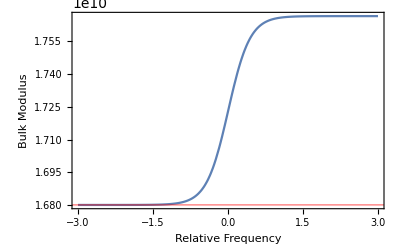

```mathematica
With[{rock="syntheticSandstone1", fluid="Water", relaxationTime=1},
Module[{Kd, μd, Km,Kf,η, ϕ, asp, ϵ},
{Kd, μd, Km, ϕ}=Normal@First@rockData[Select[#Rock==rock&],{#DryMod, #ShearMod, #MineralMod, #Porosity}&];
{ϵ, asp}=Normal@First@rockData[Select[#Rock==rock&],#SquirtParameters&][All,{#CrackDensity, #AspectRatio}&];
{Kf,η}=Normal@First@fluidData[Select[#Fluid==fluid&],{#Modulus, #Viscosity}&];
Plot[Re@isotropicModuliSquirt[ϵ,asp, relaxationTime, 10^ω,η][Kd, μd, Km, ϕ, Kf][[1]],{ω,-3,3},Frame->True,FrameLabel->{"Relative Frequency","Bulk Modulus"},GridLines->{{}, {isotropicModuliGassmann[Kd, μd, Km, ϕ, Kf][[1]]}}, GridLinesStyle->Red]
]
]
```

The case for immiscible fluids is a little more involved as viscosity and fluid moduli are now effective (mixed). The time relaxation changes at partial saturation (here 20%). The parameter q0 corresponds to patchy or uniform saturation bounds (1 being uniform, and Kg/Kw being patchy):

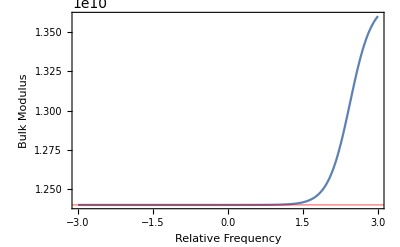

```mathematica
With[{rock="syntheticSandstone1", fluid1="Water",fluid2="Air", relTimeWater=1, λ=1/3, snwr=0., swr=0., s0=0.2, q0=.1},
Module[{Kd, μd, Km,Kf1,η1,Kf2,η2,Kfmix, ηmix,relTimemix, ϕ, asp, ϵ},
{Kd, μd, Km, ϕ}=Normal@First@rockData[Select[#Rock==rock&],{#DryMod, #ShearMod, #MineralMod, #Porosity}&];
{ϵ, asp}=Normal@First@rockData[Select[#Rock==rock&],#SquirtParameters&][All,{#CrackDensity, #AspectRatio}&];
{Kf1,η1}=Normal@First@fluidData[Select[#Fluid==fluid1&],{#Modulus, #Viscosity}&];
{Kf2,η2}=Normal@First@fluidData[Select[#Fluid==fluid2&],{#Modulus, #Viscosity}&];
{Kfmix[s_,q_],ηmix[s_,q_],relTimemix[s_,q_]}={fluidMixModulus[Kf1, Kf2, s,q],fluidMixViscosity[η1, η2, s,q,{λ,{snwr,swr}}],fluidMixRelaxation[η1, η2, s,q,{λ,{snwr,swr}}]
};
Plot[Re@isotropicModuliSquirt[ϵ,asp, relTimeWater relTimemix[s0,q0], 10^ω,ηmix[s0,q0]][Kd, μd, Km, ϕ, Kfmix[s0,q0]][[1]],{ω,-3,3},Frame->True,GridLines->{{}, {isotropicModuliGassmann[Kd, μd, Km, ϕ, Kfmix[s0,q0]][[1]]}}, GridLinesStyle->Red,FrameLabel->{"Relative Frequency","Bulk Modulus"}, PlotRange->All]
]
]
```

It is easier to see the effect of saturation and q by fixing ω and plotting against saturation of water. As q0 decreases (i.e. the saturation becomes more patchy) the characteristic relaxation time occurs in lower and lower saturation:

```mathematica
With[{rock="syntheticSandstone1", fluid1="Water",fluid2="Air", relTimeWater=1, λ=1/3, snwr=0., swr=0.,ω=0},
Module[{Kd, μd, Km,Kf1,η1,Kf2,η2,Kfmix, ηmix,relTimemix, ϕ, asp, ϵ},
{Kd, μd, Km, ϕ}=Normal@First@rockData[Select[#Rock==rock&],{#DryMod, #ShearMod, #MineralMod, #Porosity}&];
{ϵ, asp}=Normal@First@rockData[Select[#Rock==rock&],#SquirtParameters&][All,{#CrackDensity, #AspectRatio}&];
{Kf1,η1}=Normal@First@fluidData[Select[#Fluid==fluid1&],{#Modulus, #Viscosity}&];
{Kf2,η2}=Normal@First@fluidData[Select[#Fluid==fluid2&],{#Modulus, #Viscosity}&];
{Kfmix[s_,q_],ηmix[s_,q_],relTimemix[s_,q_]}:={fluidMixModulus[Kf1, Kf2, s,q],fluidMixViscosity[η1, η2, s,q,{λ,{snwr,swr}}],fluidMixRelaxation[η1, η2, s,q,{λ,{snwr,swr}}]
};
Plot[Evaluate@Table[{Re@isotropicModuliSquirt[ϵ,asp, relTimeWater relTimemix[s0,q0], 10^ω,ηmix[s0,q0]][Kd, μd, Km, ϕ, Kfmix[s0,q0]][[1]],isotropicModuliGassmann[Kd, μd, Km, ϕ, Kfmix[s0,q0]][[1]]},{q0,{1,(Kf2/Kf1)^(1/4),√(Kf2/Kf1),(Kf2/Kf1)^(3/4)}}],{s0,0,1},Frame->True,FrameLabel->{"Water Saturation","Bulk Modulus"}, PlotRange->All, PlotLabels->{"squirt","gassmann"}]
]
]
```

-Graphics-

## 3. Anisotropic Intrinsic Squirt Flow Code

```mathematica
anisotropicModuliSquirtHTI[ϵ_,ϵf_,α_,τ0_, ω_, lenrat_][λ_,μ_, ϕ_,Kf_]:=Module[
{ϕc, ϕf, ϕp, γ, γ2, ι, β, σc, ν, Kp, Kc, D1, D2, G1, G2, G3, F1, F2,k, L2,L4, τf, τm,c},
ϕc=(4 π ϵ α)/3;
ϕf=(4 π ϵf α)/3;
ϕp=ϕ-ϕc-ϕf;
Kp=(4μ)/(3 Kf);
Kc=σc/Kf;
ν=λ/(2(λ+μ));(* Poisson's ratio *)
σc=(π μ α)/(2(1-ν)); (* Crack stiffness *)

ϕp=ϕ-ϕc-ϕf;
(*
PRESSURE CALCULATION
*)
γ=(3ϕp σc (1+Kp))/(4ϕc μ (1+Kc));
γ2=γ(1-ν)/((1+ν)(1+Kp));
ι=ϕc/(ϕc+α ϕp);
β=ι ϕf/ϕc;
τf=lenrat τ0;
τm=τ0;
D1=(ι (-ⅈ+τf ω-β τm ω)+3 (1+Kc) γ2 ((1+ⅈ τf ω) (-ⅈ+τm ω)+ι (ⅈ-τf ω+β τm ω)))/(3 (1+Kc) (β (-ⅈ+(1+(-1+γ) ι) τm ω)-(-ⅈ+τf ω) (-ι+γ (-1+ι-ⅈ τm ω))));
D2=(β (-ⅈ+τm ω))/((1+Kc) (β (-ⅈ+(1+(-1+γ) ι) τm ω)-(-ⅈ+τf ω) (-ι+γ (-1+ι-ⅈ τm ω))));
G1=(τm ω)/((1+Kc) (-ⅈ+τm ω));
G2=(ⅈ (ⅈ-τf ω+β τm ω) (ι+ⅈ γ ι τm ω-3 ⅈ (1+Kc) γ2 (-1+ι) (-ⅈ+τm ω)))/(3 (1+Kc) (-ⅈ+τm ω) (β (-ⅈ+(1+(-1+γ) ι) τm ω)-(-ⅈ+τf ω) (-ι+γ (-1+ι-ⅈ τm ω))));
G3=(β (-ⅈ+γ τm ω))/((1+Kc) (β (-ⅈ+(1+(-1+γ) ι) τm ω)-(-ⅈ+τf ω) (-ι+γ (-1+ι-ⅈ τm ω))));
F1=(-3 (1+Kc) γ2 (-1+ι) (-ⅈ+τm ω)+ι (-ⅈ+γ τm ω))/(3 (1+Kc) (β (-ⅈ+(1+(-1+γ) ι) τm ω)-(-ⅈ+τf ω) (-ι+γ (-1+ι-ⅈ τm ω))));
F2=(τf ω (γ+ι-γ ι+ⅈ γ τm ω)+β (-ⅈ+(1+(-1+γ) ι) τm ω))/((1+Kc) (β (-ⅈ+(1+(-1+γ) ι) τm ω)-(-ⅈ+τf ω) (-ι+γ (-1+ι-ⅈ τm ω))));
k=λ +2/3μ;
L2=k^2+(16 μ^2)/45;
L4=k^2-(8 μ^2)/45;
c[11]=λ+2μ
-ϕc(L2/σc+32/15(1-ν)/(2-ν)μ/(π α)-(L2/σc+k)G1-((3 k^2)/σc+3k)G2-((λ k)/σc+λ)G3)
-ϕp(3/(4μ)(1-ν)/(1+ν)(3 λ^2+4λ μ+(36+20ν)/(7-5ν)μ^2)-(1+(3k)/(4μ))(3k D1+λ D2))
-ϕf(λ^2/σc-3k(λ/σc+1)F1-λ(λ/σc+1)F2);
c[33]=λ+2μ
-ϕc(L2/σc+32/15(1-ν)/(2-ν)μ/(π α)-(L2/σc+k)G1-((3 k^2)/σc+3k)G2-((λ+2μ)/σc k+λ+2μ)G3)
-ϕp(3/(4μ)(1-ν)/(1+ν)(3 λ^2+4λ μ+(36+20ν)/(7-5ν)μ^2)-(1+(3k)/(4μ))(3k D1+(λ+2μ) D2))
-ϕf((λ+2μ)^2/σc-3k((λ+2μ)/σc+1)F1-(λ+2μ)((λ+2μ)/σc+1)F2);
c[44]=μ
-ϕc(4/15 μ^2/σc(1-G1)+8/5(1-ν)/(2-ν)μ/(π α))
-ϕp(15μ(1-ν)/(7-5ν))
-ϕf(4(1-ν)/(2-ν)μ/(π α));
c[12]=λ
-ϕc(L4/σc-16/15(1-ν)/(2-ν)μ/(π α)-(L4/σc+k)G1-((3 k^2)/σc+3k)G2-((λ k)/σc+λ)G3)
-ϕp(3/(4μ)(1-ν)/(1+ν)(3 λ^2+4λ μ-(4(1+5ν))/(7-5ν)μ^2)-(1+(3k)/(4μ))(3k D1+λ D2))
-ϕf(λ^2/σc-3k(λ/σc+1)F1-λ(λ/σc+1)F2);
c[13]=λ
-ϕc(L4/σc-16/15(1-ν)/(2-ν)μ/(π α)-(L4/σc+k)G1-((3 k^2)/σc+3k)G2-((λ+μ)/σc k+λ+μ)G3)
-ϕp(3/(4μ)(1-ν)/(1+ν)(3 λ^2+4λ μ-(4(1+5ν))/(7-5ν)μ^2)-(1+(3k)/(4μ))(3k D1+(λ+μ) D2))
-ϕf((λ(λ+2μ))/σc-3k((λ+μ)/σc+1)F1-((λ(λ+2μ))/σc+λ+μ)F2);
{c[11],c[33],c[44], c[12],c[13]}
];
```

```mathematica
anisotropicDryModuliHTI[ϵ_, ϵf_, ϕ_, α_:10^-5][λ_,μ_]:=Module[{c},
c[11]=((λ+2 μ) (4 ϵ (405 (-4+3 π α) λ^4+45 (-152+123 π α) λ^3 μ+12 (-1004+1065 π α) λ^2 μ^2+4 (-2792+3735 π α) λ μ^3+80 (-56+81 π α) μ^4)+15 (3 λ+4 μ) (4 (9 (-4+3 π α) ϵf λ^3+(27+(-56+87 π α) ϵf) λ^2 μ+3 (23+56 π α ϵf) λ μ^2+6 (7+18 π α ϵf) μ^3)-9 (λ+μ) (9 λ^2+20 λ μ+36 μ^2) ϕ)))/(180 μ (λ+μ) (3 λ+4 μ) (9 λ+14 μ));
c[33]=((λ+2 μ) (4 ϵ (405 (-4+3 π α) λ^4+45 (-152+123 π α) λ^3 μ+12 (-1004+1065 π α) λ^2 μ^2+4 (-2792+3735 π α) λ μ^3+80 (-56+81 π α) μ^4)+15 (3 λ+4 μ) (4 ϵf (9 (-4+3 π α) λ^3+(-200+87 π α) λ^2 μ+8 (-46+21 π α) λ μ^2+4 (-56+27 π α) μ^3)-3 (λ+μ) (27 λ^2 ϕ+12 λ μ (-3+5 ϕ)+4 μ^2 (-14+27 ϕ)))))/(180 μ (λ+μ) (3 λ+4 μ) (9 λ+14 μ));
c[44]=μ-(16 ϵ μ (λ+2 μ) (9 λ+10 μ))/(45 (λ+μ) (3 λ+4 μ))-(16 ϵf μ (λ+2 μ))/(9 λ+12 μ)+(5 μ (λ+2 μ) (4 π α (ϵ+ϵf)-3 ϕ))/(9 λ+14 μ);
c[12]=(4 ϵ (λ+2 μ) (405 (-4+3 π α) λ^4+45 (-152+123 π α) λ^3 μ+12 (-788+615 π α) λ^2 μ^2+4 (-1064+585 π α) λ μ^3-720 π α μ^4)+15 (3 λ+4 μ) (4 ϵf (λ+2 μ) (9 (-4+3 π α) λ^3+(-56+87 π α) λ^2 μ+48 π α λ μ^2-12 π α μ^3)-3 (λ+μ) (-4 λ μ (9 λ+14 μ)+3 (λ+2 μ) (9 λ^2+20 λ μ-4 μ^2) ϕ)))/(180 μ (λ+μ) (3 λ+4 μ) (9 λ+14 μ));
c[13]=(4 ϵ (λ+2 μ) (405 (-4+3 π α) λ^4+45 (-152+123 π α) λ^3 μ+12 (-788+615 π α) λ^2 μ^2+4 (-1064+585 π α) λ μ^3-720 π α μ^4)+15 (3 λ+4 μ) (4 ϵf (λ+2 μ) (9 (-4+3 π α) λ^3+(-128+87 π α) λ^2 μ+16 (-7+3 π α) λ μ^2-12 π α μ^3)-3 (λ+μ) (-4 λ μ (9 λ+14 μ)+3 (λ+2 μ) (9 λ^2+20 λ μ-4 μ^2) ϕ)))/(180 μ (λ+μ) (3 λ+4 μ) (9 λ+14 μ));
{c[11],c[33],c[44],c[12],c[13]}
];
```

### Worked Practical Examples and Code Explanation

Code for moduli prefixed  anisotropic outputs five independent elastic moduli in the frequency domain (if the medium is viscoelastic). Haven’t coded an anisotropic Gassmann’s model yet. Situation is very similar to isotropic moduli and function is called with four input parameters, and a further six model-specific parameters. The two input parameters λ and μ differ from the isotropic case in that they need to be essentially inverted to match measurements from dry c_ij values. λ and μ correspond to the Lame and shear modulus of the effective medium which needs to be determined. As dry measurements may not always exist, a value of V_p, V_s1, V_s2 at known frequency is sometimes used to invert for λ and μ. I haven’t got code for this inversion yet but if dry moduli are available, anisotropicDryModuliHTI[CrackDensity, FractureDensity, Porosity, AspectRatio (optional)] can be used to invert λ and μ from dry values of some of the c_ij.
Such an inversion is of the form
NMinimize[Norm[anisotropicDryModuliHTI[ϵ, ϵf, ϕ][λ,μ]-{c11, c33, c44, c12, c13}]^2, {λ,μ}]
where {c11, c33, c44, c12, c13} are measured dry moduli. It needs to be pointed out that each set of combinations for crack and fracture density yields a different result for λ, μ. Once λ and μ are determined, the anisotropic viscoelastic moduli can be calculated with 
anisotropicModuliSquirtHTI[CrackDensity, FractureDensity, AspectRatio, RelaxationTime, AngularFrequency, FractureToMicrocrackRatio][EffectiveMediumLameModulus, EffectiveMediumShearModulus, Porosity, FluidModulus] 
Typical values for the crack density and fracture density parameters are between 0.001 and 0.05, the aspect ratio is usually assumed very small, in the order of 10^-5 and the ratio between fracture to microcrack size determines essentially, how much higher the crack relaxation time parameter is from the fracture time parameter. As these are standard linear solid models they are linearly superimposed. The value for relaxation time is normally adjusted from experiments. Using similar code as above we can calculate all c_ij as a function of saturation and frequency:

```mathematica
With[{rock="syntheticSandstone1", fluid1="Water",fluid2="CO2dense", relTimeWater=1, λ=1/3, snwr=0., swr=0.,(*ω=0,*) q0=1},
Module[{λm, μm,Kf1,η1,Kf2,η2,Kfmix, ηmix,relTimemix, ϕ, asp, ϵ, ϵf, ratio},
{λm, μm, ϕ}={21 10^9, 11 10^9, .08};
{ϵ, ϵf, asp, ratio}={0.01, 0.05, 10^-5, 200};
{Kf1,η1}=Normal@First@fluidData[Select[#Fluid==fluid1&],{#Modulus, #Viscosity}&];
{Kf2,η2}=Normal@First@fluidData[Select[#Fluid==fluid2&],{#Modulus, #Viscosity}&];
{Kfmix[s_,q_],ηmix[s_,q_],relTimemix[s_,q_]}:={fluidMixModulus[Kf1, Kf2, s,q],fluidMixViscosity[η1, η2, s,q,{λ,{snwr,swr}}],fluidMixRelaxation[η1, η2, s,q,{λ,{snwr,swr}}]
};
Plot[Evaluate@Table[Re@anisotropicModuliSquirtHTI[ϵ,ϵf, asp, relTimeWater relTimemix[s0,q0], 10^ω,ratio][λm,μm,ϕ,Kfmix[s0,q0]][[2]],{s0,0,1,.25}],{ω,-4,1},(* PlotStyle->White,*)Frame->True, FrameLabel->{"Scaled Frequency", "C_33"}, PlotLabels->Table[ToString[Round[s0,.01]],{s0,0,1,.25}], ImageSize->400]
]
]
```

-Graphics-

## 4. Periodic Layered Media Normal Incidence Code

```mathematica
sMatrix[r_,{dt1_, dt2_},ω_]:=Module[{a, b, θ1, θ2},
θ1=ω dt1;
θ2=ω dt2;
a = E^(I (θ1+θ2))(1-r^2 E^(-2 ⅈ θ2))/(1-r^2)//N;
b = E^(I (θ1))(2ⅈ r Sin[θ2])/(1-r^2)//N;
{{a,b},{Conjugate@b, Conjugate@a}}//N//Chop
];
```

```mathematica
generateLayered[n_Integer]:=Module[{m, rT},
m[r_,d1_,d2_,f_]:=MatrixPower[sMatrix[r,{d1, d2}/2^n/(4π), 2π f],2^n];(* divided d1, d2 by 2^n so that total thicknesses remains constant*)
rT[r2_,d1_,d2_,f_]:=Evaluate@(m[r2,d1,d2,f][[1,2]]/m[r2,d1,d2,f][[2,2]]);
ref[n][r1_,r2_,{d1_,d2_},f_]:=(r1 + rT[r2, d1, d2,f])/(1+r1 rT[r2, d1, d2,f]);
];
```

### Worked Practical Examples and Code Explanation

Code generates the frequency domain, normal incidence reflection response of a stack of 2^nlayers. Code is run in two stages: runing first generateLayered[n] creates the function ref which corresponds to the reflection response for the 2^nlayered system. This can then be used as ref[n][r1, r2, {d1,d2}, f] where r1, r2 are the reflection coefficients (can be complex) at each interface, d1,d2 is the total time thickness of each layer and f is the frequency. Changing the value of n does not affect the thicknesses . Examples:

```mathematica
n=4;
Timing[generateLayered[n]]
```

{0.005509,Null}

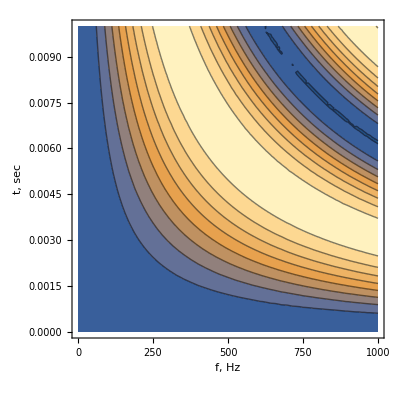

```mathematica
ContourPlot[Abs@ref[n][.8,-.1,{t/3,2t/3 },f],{f,0,1000},{t,0,.01},FrameLabel->{"f, Hz","t, sec"}]
```

## 5. Periodic Layered Media Oblique Incidence Code